## Methods

```mathematica
headerList={"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
```

```mathematica
GetData[fileName0_]:=
Module[{file = fileName0,v},
v=Import[file];
v=StringSplit[v,"\t"];
v=StringSplit[v,"\n"];
v
]
```

```mathematica
CleanDataRecord[record0_]:=
Module[{record = record0,test},
test = StringSplit[#,","]&/@record;
test =Drop[test,1];
test=ToExpression/@test;
test=PrependTo[test,headerList];
test=Dataset[Map[AssociationThread[First[test],#]&,Rest[test]]];
test
]
```

```mathematica
DisplayData[dataList0_]:=
Module[{l=dataList0,gg,a,b,c,d,labels,shortLabels,vals},
row[text_,plot_]:=Row[{text,plot},Alignment->Center];
labels=Text[Style[#,18]]&/@{"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
shortLabels = Text[Style[#,18]]&/@{"Altitude(ft)","dA/dt","Temperature(*C)"};
(*a=ListLinePlot[l[[All,1]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];*)
b=ListLinePlot[l[[All,2]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];
c=ListLinePlot[l[[All,3]],ImagePadding->{{50,50},{10,10}},ImageSize->Medium,AspectRatio->1/GoldenRatio];
vals=RateOfChange[l[[All,2]]];
d=ListPlot[vals,ImagePadding->{{50,50},{10,10}},ImageSize->Large,AspectRatio->1/GoldenRatio];
gg2=GraphicsGrid[Partition[row@@@Thread[{shortLabels,{b,d,c}}],3],Spacings->{10,20},Frame->None,ImageSize->Full];
gg2
]
```

```mathematica
RateOfChange[list0_]:=
Module[{list = list0,temp,result},
temp = list;
result={};
While[Length[temp]>1,
result=AppendTo[result,temp[[1]]-temp[[2]]];
temp=Drop[temp,1];
];
result
]
```

## Execute

{Dataset[<>],Dataset[<>]}

2

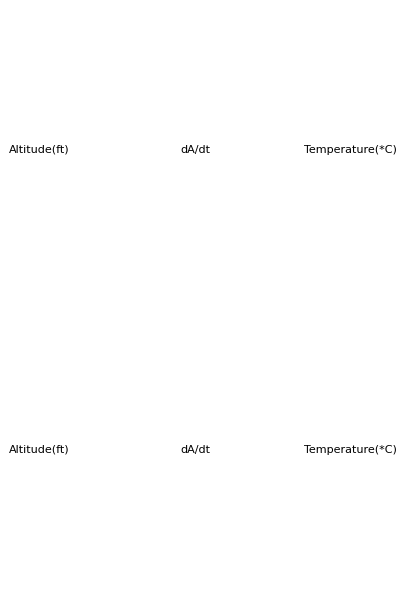

```mathematica
SetDirectory[NotebookDirectory[]];

(* change the file name to match yours *)
fileName="ZANE.TXT";

(* change the directory to match the date data was collected. Format MM_DD_YY *)
dir = "09_28_18";

file = StringJoin["Data/",dir,"/",fileName];
data=GetData[file];
cleanData=CleanDataRecord/@data
cleanData//Length
graphs=DisplayData/@cleanData;
graphs//TableForm
```